# Лабораторная работа 11

## Конструкторы точка, вектор

```mathematica
(*точка*)
ClearAll[kmPoint];
(*конструкторы*)
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord]
kmPoint[id_String,coord:{_,_}]:=kmPoint[km, id,coord]
kmPoint[{ϕ_,r_},"pol"]:=kmPoint[km,"",{r*Cos[ϕ],r*Sin[ϕ]} ]
kmPoint[id_String,{ϕ_,r_},"pol"]:=kmPoint[km,id,{r*Cos[ϕ],r*Sin[ϕ]}]
(*запросы свойств*)
kmPoint[km,id_String,___,coord_List,___]["coord"]:=coord;
kmPoint[km,id_String,___]["id"]:=If[id=="","Точка",id];
kmPoint[km,id_String,___,coord_List,___]["coord"]:=coord;
kmPoint[km,id_String,___]["id"]:=If[id=="","Точка",id];
NamedQ[kmPoint[km,id_String,__]]^:=id≠""
```

```mathematica
(*вектор*)
ClearAll[kmVector];
(*конструкторы*)
kmVector[id_String, coord:{_,_}]:=kmVector[km,id,coord]
kmVector[ coord:{_,_}]:=kmVector[km,"",coord]
kmVector[id_String, P0_kmPoint, P1_kmPoint]:=kmVector[id,P0@"coord"-P1@"coord"]
kmVector[ P0_kmPoint, P1_kmPoint]:=kmVector[If[And@@NamedQ/@{P0,P1},StringJoin[P0@"id",P1@"id"]," "],P0@"coord"-P1@"coord"]
kmVector[id_String,v_kmVector,d_]:=kmVector[id,v@"coord"*d]
kmVector[v_kmVector,d_]:=kmVector[If[And@@NamedQ/@{P0,P1},StringJoin[P0@"id",P1@"id"]," "],v@"coord"*d]
(*запросы свойств*)
kmVector[km,id_String,__]["id"]:=If[id=="","Vector",id]
kmVector[km,__,coord:{_,_}]["coord"]:=coord;
kmVector[km,__,coord:{_,_}]["length"]:=√(coord.coord);
kmVector[km,__,coord:{_,_}]["ort"]:=kmVector[coord/(√(coord.coord))]
NamedQ[kmVector[km,id_String,__]]^:=id≠""
NamedQ[kmLine[km,id_String,__]]^:=id≠""
```

## Задание 1 Базовые конструкторы

```mathematica
kmLine[km,id_String, {A_,B_,C_}]
```

kmLine[km,id_String,{A_,B_,C_}]

```mathematica
kmLine[id_String, A_.x_+B_.y_+C_.==0,{x_Symbol,y_Symbol}]:=kmLine[km,id,{A,B,C}]/;¬PossibleZeroQ[Abs@A+Abs@B];
```

```mathematica
kmLine["L1",5f-a==0,{f,a}]
```

kmLine[km,L1,{5,-1,0}]

```mathematica
kmLine["L1",5f-a==0,{a,f}]
```

kmLine[km,L1,{-1,5,0}]

```mathematica
kmLine["L2",5f==0,{f,a}]
```

kmLine[L2,5 f==0,{f,a}]

```mathematica
MatchQ[5f==0,A_.x_+B_.y_+C_.==0]
```

False

```mathematica
MatchQ[5f+9==0,A_.x_+B_.y_+C_.==0]
```

True

```mathematica
kmLine["L2",5f+7==0,{f,a}]
```

kmLine[L2,7+5 f==0,{f,a}]

```mathematica
kmLine[id_String,A_.x_+C_.==0,{x_Symbol, _Symbol}]:=kmLine[km,id,{A,0,C}];
```

```mathematica
kmLine[id_String,B_.y_+C_.==0,{_Symbol, y_Symbol}]:=kmLine[km,id,{0,B,C}];
```

```mathematica
kmLine["L2",5f+7==0,{f,a}]
```

kmLine[km,L2,{5,0,7}]

```mathematica
kmLine["L2",5f==0,{f,a}]
```

kmLine[km,L2,{5,0,0}]

```mathematica
kmLine["L2",5f==0,{a,f}]
```

kmLine[km,L2,{0,5,0}]

```mathematica
kmLine[L3,False,{f,a}]
```

kmLine[L3,False,{f,a}]

```mathematica
kmLine[km,"",{A_,B_,_}]:=Abort[]/;PossibleZeroQ[Abs@A+Abs@B]
```

```mathematica
kmLine[km,"",{0,0.,3}]
```

$Aborted

## Задание 2

```mathematica
kmLine[equ:(__==0),vars:{_Symbol,_Symbol}]:=kmLine["",equ,vars]
```

```mathematica
kmLine[5f+3==0,{f,a}]
```

kmLine[km,,{5,0,3}]

```mathematica
(*1 sposob*)
```

```mathematica
{P,P0}=kmPoint/@{{x,y},{p0x,p0y}}
```

{kmPoint[km,,{x,y}],kmPoint[km,,{p0x,p0y}]}

```mathematica
V=kmVector[{Vx,Vy}]
```

kmVector[km,,{Vx,Vy}]

```mathematica
{V@"coord",P@"coord"-P0@"coord"}//MatrixForm
```

(Vx | Vy
-p0x+x | -p0y+y)

```mathematica
Det[{V@"coord",P@"coord"-P0@"coord"}]==0
```

-p0y Vx+p0x Vy-Vy x+Vx y==0

```mathematica
kmLine[id_String,P0_kmPoint,Dir_kmVector]:=kmLine[id,Det[{Dir@"coord",{x,y}-P0@"coord"}]==0,{x,y}]
```

```mathematica
kmLine["L",kmPoint[{5,5}],kmVector[{-1,1}]]
```

kmLine[km,L,{-1,-1,10}]

```mathematica
(*2 sposob*)
```

A = -Vy,
 B = Vx,
  C = -p0y Vx + p0x Vy.

```mathematica
({{0, -1}, {1, 0}}).V@"coord"(*norm vector*)
```

{-Vy,Vx}

Значение параметра C, записанное в (4.9), может быть вычислено с
использованием скалярного произведения радиус - вектора точки p0 ∈ l и
вектора нормали N, а именно C = -(p0, N).

```mathematica
-(({{0, -1}, {1, 0}}).V@"coord").P0@"coord"
```

-p0y Vx+p0x Vy

```mathematica
Append[#,-#.P0@"coord"]&[({{0, -1}, {1, 0}}).V@"coord"]
```

{-Vy,Vx,-p0y Vx+p0x Vy}

```mathematica
kmLine[id_String,P0_kmPoint,Dir_kmVector]:=kmLine[km,id,Append[#,-#.P0["coord"]]&[({{0, -1}, {1, 0}}).Dir@"coord"]]
```

```mathematica
kmLine["",P0,V]
```

kmLine[km,,{-Vy,Vx,-p0y Vx+p0x Vy}]

```mathematica
kmLine["",kmPoint[{2,3}],kmVector[{10,20}]]
```

kmLine[km,,{-20,10,10}]

```mathematica
kmLine[P_kmPoint,Dir_kmVector]:=kmLine[If[And@@(NamedQ/@{P,Dir}),StringJoin[P@"id",Dir@"id"],""],P,Dir]
```

```mathematica
kmLine[P0,V]
```

kmLine[km,,{-Vy,Vx,-p0y Vx+p0x Vy}]

```mathematica
P1=kmPoint["A",{Ax,Ay}]
```

kmPoint[km,A,{Ax,Ay}]

```mathematica
a=kmVector["a",{ax,ay}]
```

kmVector[km,a,{ax,ay}]

```mathematica
kmLine[P1,a]
```

kmLine[km,Aa,{-ay,ax,Ax ay-ax Ay}]

```mathematica
NamedQ[P1]
```

True

```mathematica
kmLine[id_String,P0_kmPoint,P1_kmPoint]:=kmLine[id,P0,kmVector[P1,P0]]
```

```mathematica
kmLine["LL",kmPoint[{2,3}],kmPoint[{10,20}]]
```

kmLine[km,LL,{-17,8,10}]

```mathematica
kmLine[P0_kmPoint,P1_kmPoint]:=kmLine[If[And@@(NamedQ/@{P0,P1}),StringJoin[P0@"id",P1@"id"],""],P0,P1]
```

```mathematica
kmLine[kmPoint["a",{2,3}],kmPoint["b",{10,20}]]
```

```mathematica
as=kmVector[{1,3}]
```

kmVector[km,,{1,3}]

## Задание

```mathematica
V=kmVector[{5,2}]
```

kmVector[km,,{5,2}]

```mathematica
NLeft=kmVector[({{0, -1}, {1, 0}}).V@"coord"]
```

kmVector[km,,{-2,5}]

```mathematica
NRight=kmVector[({{0, 1}, {-1, 0}}).V@"coord"]
```

kmVector[km,,{2,-5}]

```mathematica
NLeft=kmVector[{Nx,Ny}]
```

kmVector[km,,{Nx,Ny}]

```mathematica
V=kmVector[({{0, 1}, {-1, 0}}).NLeft@"coord"]
```

kmVector[km,,{Ny,-Nx}]

```mathematica
kmLine[id_String,P0_kmPoint,N_kmVector]:=kmLine[id,P0,kmVector[({{0, 1}, {-1, 0}}).N@"coord"]]
```

```mathematica
kmLine[P0_kmPoint,N_kmVector]:=kmLine[If[And@@(NamedQ/@{P0,N}),StringJoin[P0@"id",N@"id"],""],P0,N]
```

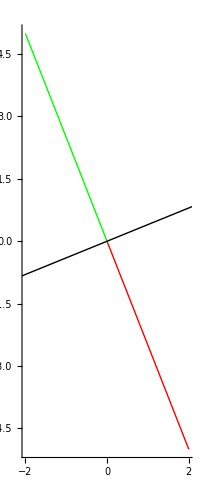

```mathematica
Graphics[{InfiniteLine[{{0,0},V@"coord"}],Red,Line[{{0,0},NRight@"coord"}],Green,Line[{{0,0},NLeft@"coord"}]},Axes->True]
```

## Свойства

```mathematica
kmLine[km,id_String,__]["id"]:=If[id=="","Прямая",id];
```

```mathematica
kmLine[km,__, {A_.,B_.,C_.}]["coef"]:={A,B,C};
```

```mathematica
kmLine[km,__, {A_.,C_.}]["coef"]:={A,C}
```

```mathematica
kmLine[km,__, {B_.,C_.}]["coef"]:={B,C}
```

```mathematica
kmLine["lol", x+9==0, {x,y}]["coef"]
```

{1,0,9}

```mathematica
kmLine[km, id_String, coef:{A_.,B_.,C_.}]["equ"]:=(A x+B y + C ==0)
```

```mathematica
kmLine[km,___, coef:{A_.,B_.,C_.} ]["norm"]:=kmVector[{A,B}]
```

```mathematica
kmLine[km,___, coef:{A_.,B_.,C_.} ]["dir"]:=kmVector[{-B,A}]
```

## Задание 4.17

```mathematica
L=kmLine[km, "", {17,-8,-10}]
```

kmLine[km,,{17,-8,-10}]

```mathematica
L@"coef".{x0,y,1}==0
```

-10-8 y+17 x0==0

```mathematica
First@Solve[L@"coef".{x0, y,1}==0,y]
```

{y→1/8 (-10+17 x0)}

```mathematica
{x0,y}/.First@Solve[L@"coef".{x0, y,1}==0,y]
```

{x0,1/8 (-10+17 x0)}

```mathematica
Table[{x0,y}/.First@Solve[L@"coef".{x0, y,1}==0,y],{x0,{-1,1}}]
```

{{-1,-27/8},{1,7/8}}

```mathematica
Attributes[Table]
```

{HoldAll,Protected}

```mathematica
Table[{x0,y}/.First@Solve[L@"coef".{x0,y,1}==0],{x0,{-1,1}}]
```

{{-1,-27/8},{1,7/8}}

```mathematica
Ly = kmLine[km, "", {0,-8,-10}]
```

kmLine[km,,{0,-8,-10}]

```mathematica
Table[{x0,y}/.First@Solve[Ly@"coef".{x0,y,1}==0],{x0,{-1,1}}]
```

{{-1,-5/4},{1,-5/4}}

```mathematica
Lx=kmLine[km, "", {17,0,-10}]
```

kmLine[km,,{17,0,-10}]

```mathematica
Lx@"coef".{1,y,1}==0
```

False

```mathematica
If[Apply[Less, Abs@L["coef"]⟦{1,2}⟧],Table[{x, y}/.First@Solve[L@"coef".{x, y,1}==0],{x,{-1,1}}],Table[{x, y}/.First@Solve[L["coef"].{x, y,1}==0],{y,{-1,1}}]]
```

{{2/17,-1},{18/17,1}}

```mathematica
ClearAll[kmGetTwoLinePoints];
```

```mathematica
kmGetTwoLinePoints[Line_kmLine]:=Map[kmPoint,If[Apply[Less, Abs@Line["coef"]⟦{1,2}⟧],Table[{x, y}/.First@Solve[Line@"coef".{x, y,1}==0],{x,{-1,1}}],Table[{x, y}/.First@Solve[Line["coef"].{x, y,1}==0],{y,{-1,1}}]]]
```

```mathematica
kmGetTwoLinePoints/@{L,Lx,Ly}
```

{{kmPoint[km,,{2/17,-1}],kmPoint[km,,{18/17,1}]},{kmPoint[km,,{10/17,-1}],kmPoint[km,,{10/17,1}]},{kmPoint[km,,{-1,-5/4}],kmPoint[km,,{1,-5/4}]}}

```mathematica
ClearAll[ kmGraphics2D];
```

```mathematica
kmGraphics2D[ point_List,opts___]:=Graphics[ ReplaceAll[ point,{P_kmPoint :>Tooltip[ Point@P@"coord",Style[Format[P,StandardForm],Large]],L_kmLine:> Tooltip[ InfiniteLine@ Through @kmGetTwoLinePoints[ L]@ "coord",Style[ Format[ L,StandardForm],Large]]}],opts]
```

```mathematica
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

```mathematica
{L1,L2}=kmLine[km, "",#]&/@{{1,5,3},{-2,3,-1}}
```

{kmLine[km,,{1,5,3}],kmLine[km,,{-2,3,-1}]}

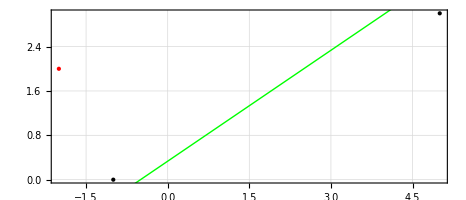

```mathematica
kmGraphics2D[{{PointSize@Large, P1,P2,Red,P3},{Thick,Blue,L1,Green, L2}},Frame ->True,GridLines->Automatic, PlotRange ->All]
```

## Задание 5.1

```mathematica
ClearAll[L1,L2];
```

```mathematica
{L1,L2}=MapThread[kmLine[#1,#2]&,{{x+5y+3==0,-2x+3y-1==0},{{x,y},{x,y}}}]
```

{kmLine[km,,{1,5,3}],kmLine[km,,{-2,3,-1}]}

```mathematica
{L1,L2}//Map[#["coef"].{x,y,1}==0&,#]&
```

{3+x+5 y==0,-1-2 x+3 y==0}

```mathematica
{L1,L2}//Map[#["coef"].{x,y,1}==0&,#]&//First@Solve[#]&
```

{x→-14/13,y→-5/13}

```mathematica
{L1,L2}//Map[#["coef"].{x,y,1}==0&,#]&//First@Solve[#]&//({x,y}/.#)&
```

{-14/13,-5/13}

```mathematica
{L1,L2}//Map[#["coef"].{x,y,1}==0&,#]&//First@Solve[#]&//({x,y}/.#)&//kmPoint
```

kmPoint[km,,{-14/13,-5/13}]

```mathematica
kmPoint[L1_kmLine,L2_kmLine]:=kmPoint[{x,y}]/.First@Solve[Map[#["coef"].{x,y,1}==0&,{L1,L2}]];
```

```mathematica
L3=kmLine[km,"",{4,4,-12}]
```

kmLine[km,,{4,4,-12}]

```mathematica
{P12,P23,P31}=
kmPoint @@@{{L1,L2},{L2,L3},{L3,L1}}
```

{kmPoint[km,,{-14/13,-5/13}],kmPoint[km,,{8/5,7/5}],kmPoint[km,,{9/2,-3/2}]}

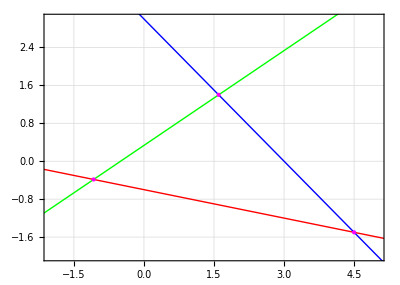

```mathematica
kmGraphics2D[{
{Thick,Red,L1,Green,L2,Blue,L3},{PointSize@Large,Magenta,P12,P23,P31}}
,Frame ->True,GridLines ->Automatic, PlotRange->{{-2,5},{-2,3}}]
```

```mathematica
kmVector["⊥",vec_kmVector]:=kmVector[({{0, -1}, {1, 0}}).vec@"coord"]
```

```mathematica
kmLine[P_kmPoint, L_kmLine]:=kmLine[P,L["norm"]]
```